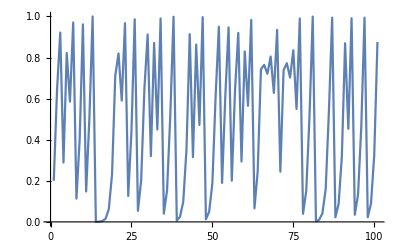

```mathematica
ListLinePlot[NestList[4#(1-#)&,0.2,100]]
```

```mathematica
Nest[1+1/#&,1,30]//N
```

1.61803

```mathematica
Table[RandomReal[{-1,1}],10]
```

{-0.509622,0.569809,-0.647539,-0.55786,-0.61615,-0.157716,0.100341,0.279675,0.356458,0.875709}

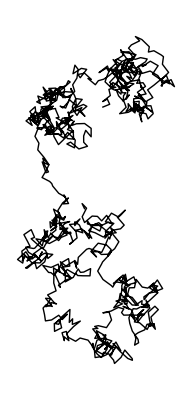

```mathematica
Graphics[Line[NestList[#+{RandomReal[{-1,1}],RandomReal[{-1,1}]}&,{0,0},1000]]]
```

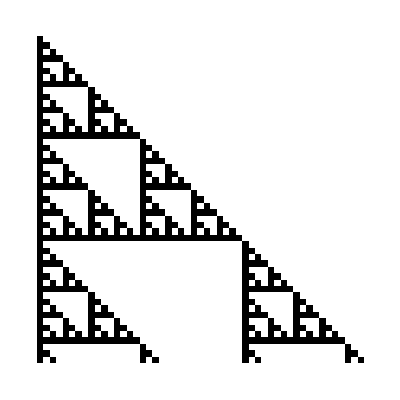

```mathematica
NestList[Mod[Join[{0},#]+Join[#,{0}],2]&,{1},50]//ArrayPlot
```

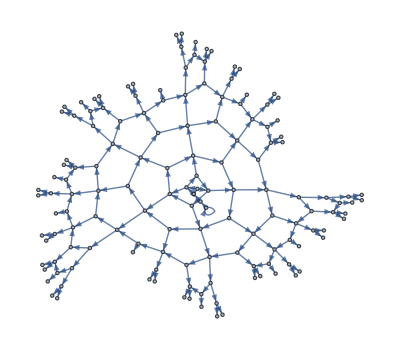

```mathematica
NestGraph[{#+1,2#}&,0,10]
```

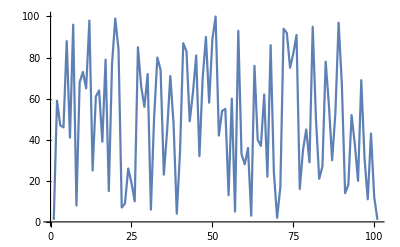

```mathematica
ListLinePlot@NestList[Mod[59#,101]&,1,100]
```

```mathematica
Graphics3D[Line[NestList[#+{RandomReal[{-1,1}],RandomReal[{-1,1}],RandomReal[{-1,1}]}&,{0,0,0},1000]]]
```

-Graphics3D-

```mathematica
3≤4
```

True

```mathematica
Select[Prime[#]&/@Range[100],Last[IntegerDigits[#]]<3&]
```

{2,11,31,41,61,71,101,131,151,181,191,211,241,251,271,281,311,331,401,421,431,461,491,521,541}

```mathematica
Select[RomanNumeral[#]&/@Range[100],!MemberQ[Characters[#],"I"]&]
```

{V,X,XV,XX,XXV,XXX,XXXV,XL,XLV,L,LV,LX,LXV,LXX,LXXV,LXXX,LXXXV,XC,XCV,C}

```mathematica
Select[RomanNumeral[#]&/@Range[1000],PalindromeQ]
```

{I,II,III,V,X,XIX,XX,XXX,L,C,CXC,CC,CCC,D,M}

```mathematica
Select[IntegerName[#]&/@Range[100],StringTake[#,1]==StringTake[StringReverse[#],1]&]
```

{nineteen,twenty-eight,thirty-eight,eighty-one,eighty-three,eighty-five,eighty-nine,ninety-seven}

```mathematica
Select[TextWords[WikipediaData["words"]],StringLength[#]>15&]
```

{Definitions/meanings,orthographically,multiple-morpheme,lavarse.Japanese,Proto-Indo-European,978-0-19-924370-9,978-0-521-28492-9,978-0-521-40179-1,978-0-415-23377-4,978-0-415-29893-3,978-0-521-52563-3,978-0-19-870002-9}

```mathematica
NestList[If[EvenQ[#],#/2,3#+1]&,1000,10]
```

{1000,500,250,125,376,188,94,47,142,71,214}

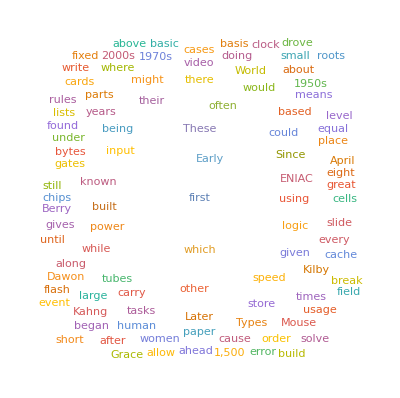

```mathematica
WordCloud@Select[TextWords[WikipediaData["computers"]],StringLength[#]==5&]
```

```mathematica
Select[WordList[],StringLength[#]>6&&StringTake[#,3]==StringTake[StringReverse[#],3]&&!PalindromeQ[#]&]
```

{despised,detected,detested,drainboard,foolproof,lackadaisical,marjoram,revolver}

```mathematica
Select[WordList[],StringLength[#]==10&&Total[LetterNumber[#]]==100&]
```

{accumulate,alienation,answerable,apoplectic,aquamarine,bewitching,censurable,ceramicist,chastening,chimpanzee,clinically,collecting,condensate,congenital,conjugated,connivance,declension,deliquesce,demobilize,demodulate,denominate,diagonally,discipline,discommode,egoistical,emasculate,embodiment,emendation,empathetic,fatalistic,fatherhood,geographer,hemoglobin,inadequacy,interbreed,leveraging,liberalism,likelihood,martingale,mercantile,meridional,neoclassic,paramecium,plebiscite,potbellied,quadrangle,reciprocal,regimented,reschedule,researcher,scoreboard,septicemia,shibboleth,sleepyhead,stagecraft,stalemated,temperance,thickening,threatened,uncombined,unmodified}

```mathematica
If[Last[IntegerDigits[#]]==3,0,#]&/@Range[25]
```

{1,2,0,4,5,6,7,8,9,10,11,12,0,14,15,16,17,18,19,20,21,22,0,24,25}

```mathematica
StringTake["Helo",-3]
```

elo

```mathematica
Select[Range[1000],Mod[#,7]==1&&Mod[#,8]==1&]
```

{1,57,113,169,225,281,337,393,449,505,561,617,673,729,785,841,897,953}

```mathematica
If[Mod[#,3]==0,If[Mod[#,5]==0,Red,Black],If[Mod[#,5]==0,White,#]]&/@Range[100]
```

{1,2,GrayLevel[0],4,GrayLevel[1],GrayLevel[0],7,8,GrayLevel[0],GrayLevel[1],11,GrayLevel[0],13,14,RGBColor[1, 0, 0],16,17,GrayLevel[0],19,GrayLevel[1],GrayLevel[0],22,23,GrayLevel[0],GrayLevel[1],26,GrayLevel[0],28,29,RGBColor[1, 0, 0],31,32,GrayLevel[0],34,GrayLevel[1],GrayLevel[0],37,38,GrayLevel[0],GrayLevel[1],41,GrayLevel[0],43,44,RGBColor[1, 0, 0],46,47,GrayLevel[0],49,GrayLevel[1],GrayLevel[0],52,53,GrayLevel[0],GrayLevel[1],56,GrayLevel[0],58,59,RGBColor[1, 0, 0],61,62,GrayLevel[0],64,GrayLevel[1],GrayLevel[0],67,68,GrayLevel[0],GrayLevel[1],71,GrayLevel[0],73,74,RGBColor[1, 0, 0],76,77,GrayLevel[0],79,GrayLevel[1],GrayLevel[0],82,83,GrayLevel[0],GrayLevel[1],86,GrayLevel[0],88,89,RGBColor[1, 0, 0],91,92,GrayLevel[0],94,GrayLevel[1],GrayLevel[0],97,98,GrayLevel[0],GrayLevel[1]}

```mathematica
Select[EntityList[EntityClass["Planet",All]],#["Mass"]>Entity["Planet","Earth"]["Mass"]&]
```

{Jupiter,Saturn,Uranus,Neptune}

```mathematica
Table[If[Mod[i,j]==0,1,0],{i,50},{j,50}]//ArrayPlot
```

-Graphics-

```mathematica
Table[If[MemberQ[IntegerDigits[i],5]||MemberQ[IntegerDigits[j],5],0,1],{i,100},{j,100}]//ArrayPlot
```

-Graphics-

```mathematica
Join[{1,2},{3,4}]
```

{1,2,3,4}

```mathematica
{1,2}~Join~{3,4}
```

{1,2,3,4}

```mathematica
5~Plus~3
```

```mathematica
Prime/@Range[10]
```

{2,3,5,7,11,13,17,19,23,29}

```mathematica
Range[3,8]
```

{3,4,5,6,7,8}

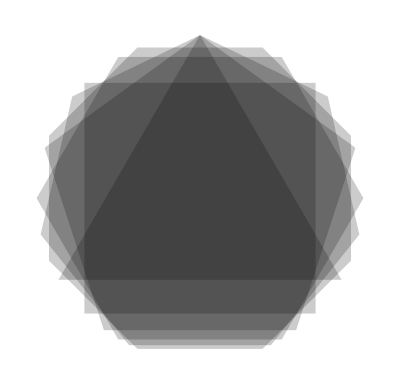

```mathematica
Graphics[{Opacity[0.2],RegularPolygon/@Range[3,8]}]
```

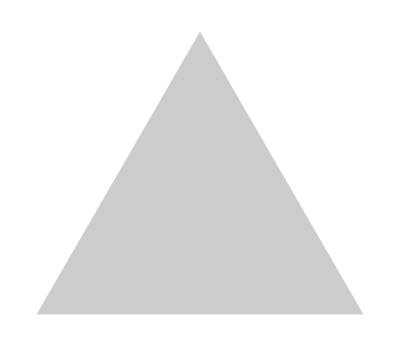
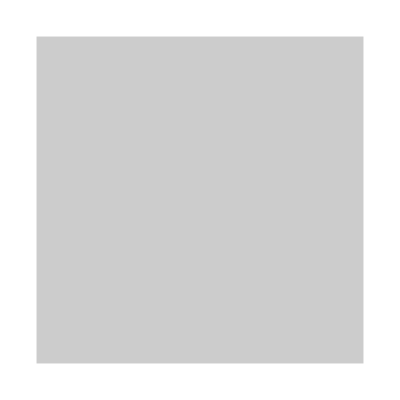
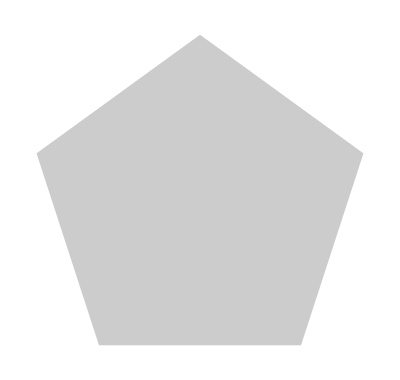
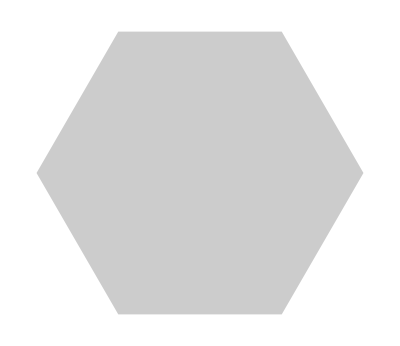
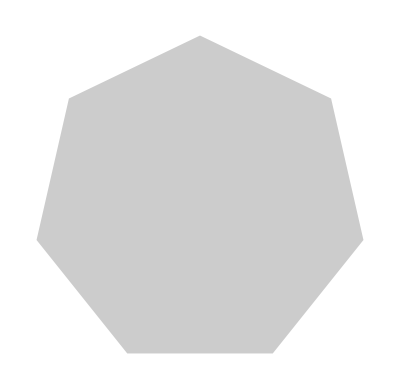
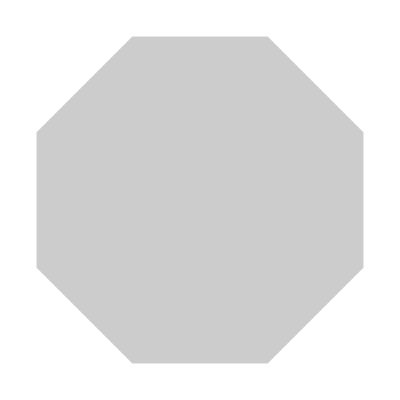

```mathematica
Graphics[{Opacity[0.2],RegularPolygon[#]}]&/@Range[3,8]
```

```mathematica
FoldList[ImageAdd,Graphics[{Opacity[0.2],RegularPolygon[#]}]&/@Range[3,8]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Thread
```